```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Tscancnew=1000 Join[Table[i,{i,0.15,0.16,0.002}],Table[i,{i,0.162,0.3,0.003}]];
```

```mathematica
ImAsMass[[;;40]]
```

{{3.07256,3.59416},{3.0699,3.58563},{3.06722,3.57702},{3.06452,3.568},{3.0618,3.55879},{3.05908,3.54935},{3.05634,3.53969},{3.05222,3.52468},{3.04809,3.5112},{3.04396,3.49786},{3.03981,3.48475},{3.03566,3.47246},{3.03151,3.46009},{3.02736,3.44589},{3.0232,3.43184},{3.01904,3.41767},{3.01487,3.40356},{3.0107,3.38958},{3.00653,3.37583},{3.00236,3.36208},{2.99826,3.34884},{2.99427,3.33623},{2.99028,3.32385},{2.98627,3.31177},{2.98225,3.30009},{2.97822,3.28856},{2.97419,3.27791},{2.97013,3.27125},{2.96607,3.2657},{2.962,3.26055},{2.95791,3.25579},{2.95383,3.25144},{2.9497,3.24762},{2.94557,3.24429},{2.94141,3.24164},{2.93724,3.24047},{2.93304,3.24637},{2.9288,3.35443},{2.92452},{2.9202}}

```mathematica
ImRegMass=Import["spectraldata/Tscan/cc_regIm/results/wrfitcc.dat"];
ImUnRegMass=Import["spectraldata/Tscan/cc_all/results/wrfitcc.dat"];
ImAsMass=Import["spectraldata/Tscan/cc_asIm/results/wrfitcc.dat"];
```

```mathematica
ImRegWidth=Import["spectraldata/Tscan/cc_regIm/results/gfitcc.dat"];
ImUnRegWidth=Import["spectraldata/Tscan/cc_all/results/gfitcc.dat"];
ImAsWidth=Import["spectraldata/Tscan/cc_asIm/results/gfitcc.dat"];
```

```mathematica
ImRegArea=Import["spectraldata/Tscan/cc_regIm/results/areafitcc.dat"];
ImUnRegArea=Import["spectraldata/Tscan/cc_all/results/areafitcc.dat"];
ImAsArea=Import["spectraldata/Tscan/cc_asIm/results/areafitcc.dat"];
```

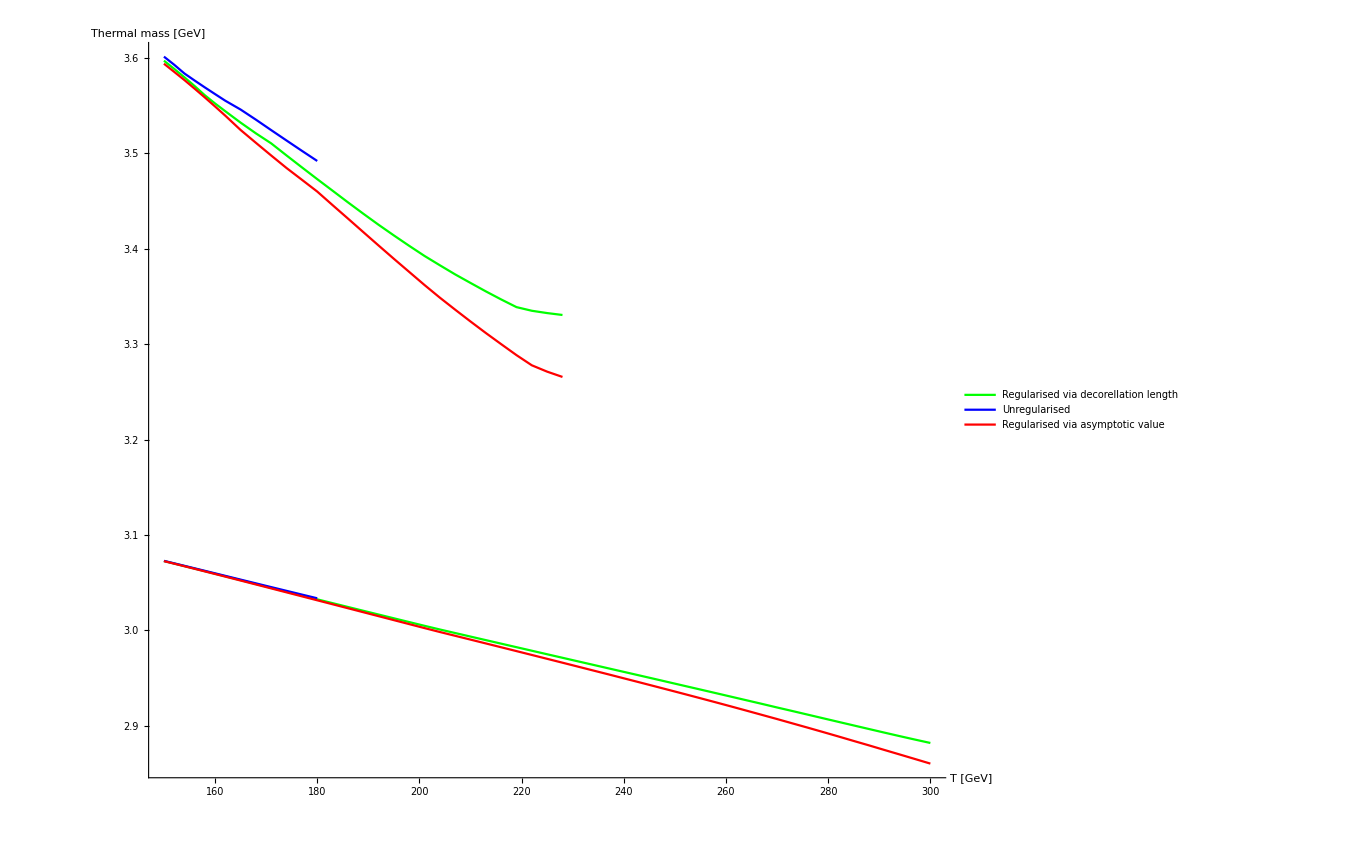

```mathematica
ListPlot[{Transpose[{Tscancnew,ImRegMass[[All,1]]}],Transpose[{Tscancnew[[;;13]],ImUnRegMass[[All,1]]}],Transpose[{Tscancnew,ImAsMass[[All,1]]}],Transpose[{Tscancnew[[;;29]],ImRegMass[[;;29]][[All,2]]}],Transpose[{Tscancnew[[;;13]],ImUnRegMass[[All,2]]}],Transpose[{Tscancnew[[;;29]],ImAsMass[[;;29]][[All,2]]}]},Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Thermal mass [GeV]"},PlotStyle->{{Green,Thick},{Blue,Thick},{Red,Thick},{Green,Thick},{Blue,Thick},{Red,Thick}},PlotLegends-> {Style["Regularised via decorellation length",25],Style["Unregularised",25],Style["Regularised via asymptotic value",25]},ImageSize->{1000,1000}]
```

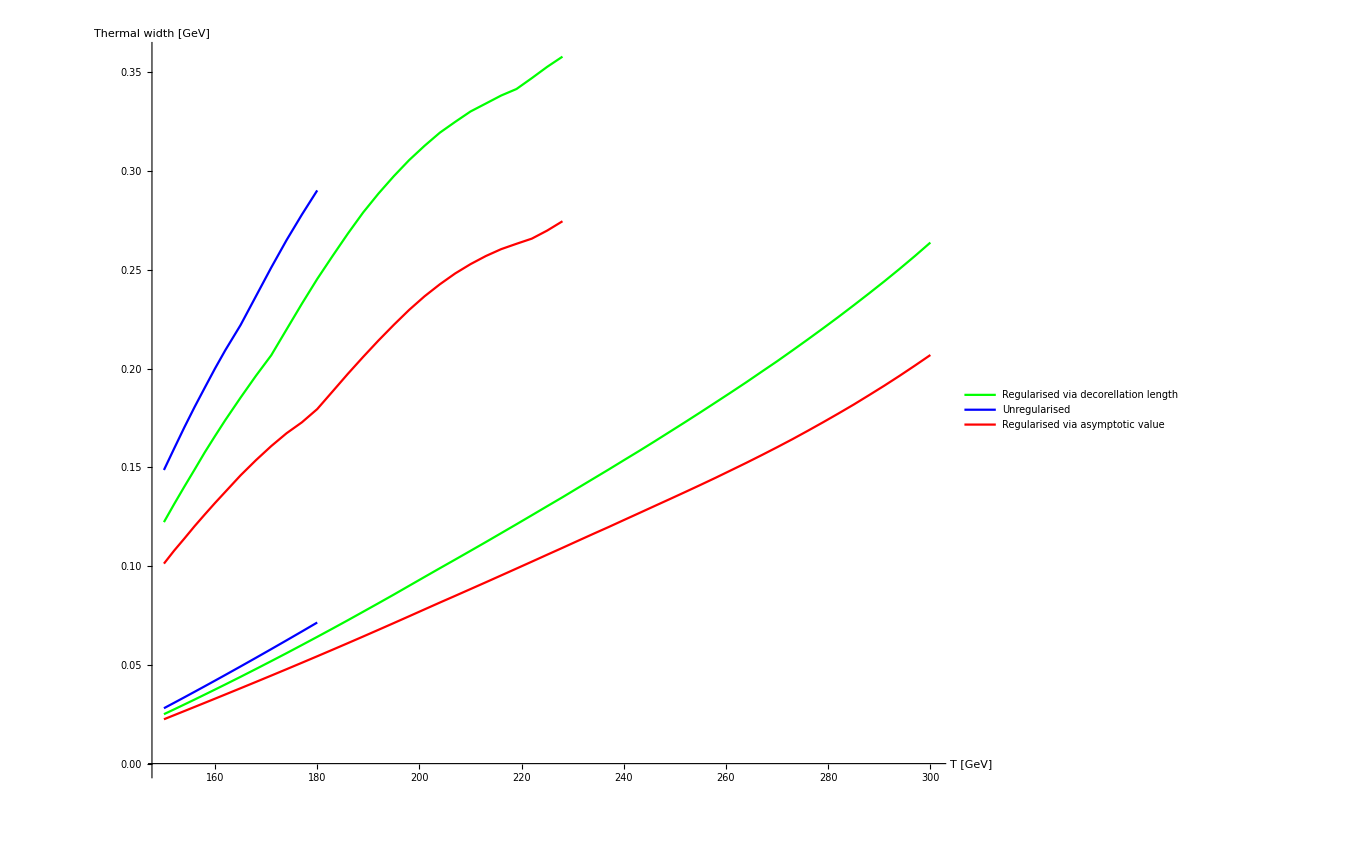

```mathematica
ListPlot[{Transpose[{Tscancnew,ImRegWidth[[All,1]]}],Transpose[{Tscancnew[[;;13]],ImUnRegWidth[[All,1]]}],Transpose[{Tscancnew,ImAsWidth[[All,1]]}],Transpose[{Tscancnew[[;;29]],ImRegWidth[[;;29]][[All,2]]}],Transpose[{Tscancnew[[;;13]],ImUnRegWidth[[All,2]]}],Transpose[{Tscancnew[[;;29]],ImAsWidth[[;;29]][[All,2]]}]},Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Thermal width [GeV]"},PlotStyle->{{Green,Thick},{Blue,Thick},{Red,Thick},{Green,Thick},{Blue,Thick},{Red,Thick}},PlotLegends-> {Style["Regularised via decorellation length",25],Style["Unregularised",25],Style["Regularised via asymptotic value",25]},ImageSize->{1000,1000}]
```

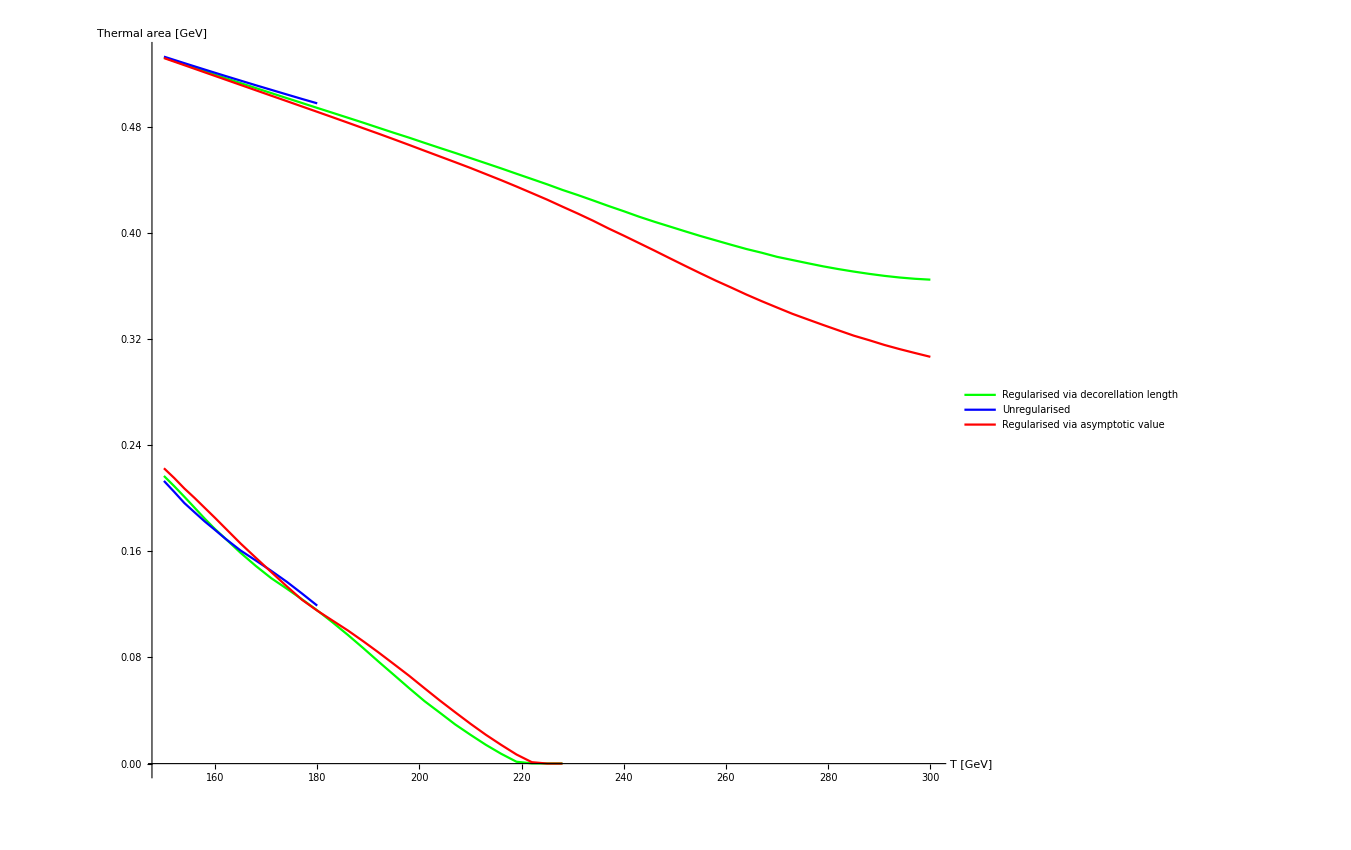

```mathematica
ListPlot[{Transpose[{Tscancnew,ImRegArea[[All,1]]}],Transpose[{Tscancnew[[;;13]],ImUnRegArea[[All,1]]}],Transpose[{Tscancnew,ImAsArea[[All,1]]}],Transpose[{Tscancnew[[;;29]],ImRegArea[[;;29]][[All,2]]}],Transpose[{Tscancnew[[;;13]],ImUnRegArea[[All,2]]}],Transpose[{Tscancnew[[;;29]],ImAsArea[[;;29]][[All,2]]}]},Joined->True,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Thermal area [GeV]"},PlotStyle->{{Green,Thick},{Blue,Thick},{Red,Thick},{Green,Thick},{Blue,Thick},{Red,Thick}},PlotLegends-> {Style["Regularised via decorellation length",25],Style["Unregularised",25],Style["Regularised via asymptotic value",25]},ImageSize->{1000,1000}]
```

```mathematica
tab=Import["spectraldata/Tscan/AsReg/cc/swccT150spectra.dat"];
```

```mathematica
tab=tab/.{a_,b_}:>{a,b/a^2};
```

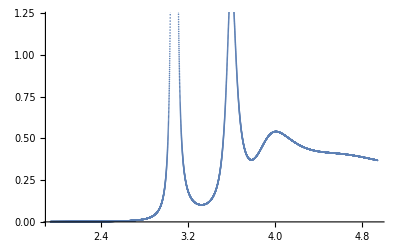

```mathematica
ListPlot[tab]
```

```mathematica
tab[[;;10]]
```

{{1.93838,-0.00123383},{1.93867,-0.00123414},{1.93897,-0.00123448},{1.93926,-0.0012348},{1.93955,-0.00123513},{1.93985,-0.00123545},{1.94014,-0.00123577},{1.94044,-0.0012361},{1.94073,-0.00123643},{1.94102,-0.00123675}}